# 数据集列归一化与聚类示例

```mathematica
file="userid_data.csv";
```

```mathematica
data0=Import@file;
```

```mathematica
{head,data}={First@data0,Rest@data0};
```

```mathematica
asso=GroupBy[data,First->Rest,First];
```

```mathematica
c=FindClusters[asso[[1;;100]],10];
```

```mathematica
Length/@c
```

{87,1,4,1,2,1,1,1,1,1}

```mathematica
data1=AssociationThread[head->#]&/@data;
```

```mathematica
dataset=Dataset@data1;
```

## 看数据

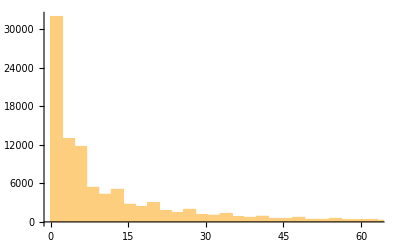

```mathematica
data[[All,2]]//Histogram
```

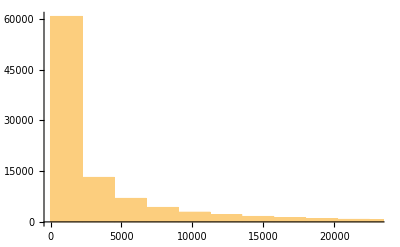

```mathematica
data[[All,3]]//Histogram
```

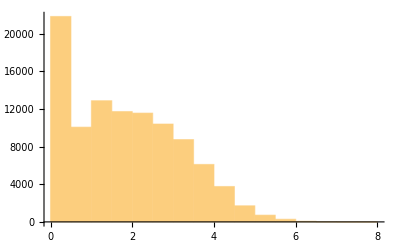

```mathematica
Log[data[[All,2]]]//Histogram
```

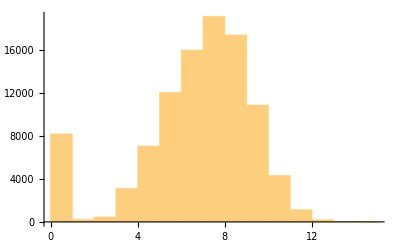

```mathematica
Log[data[[All,3]]]//Histogram
```

## Dataset

```mathematica
fields=Rest@head
```

{paidordercnt,paidorderamt}

```mathematica
(minMax[#]=Normal@dataset[MinMax,#])&/@fields
```

{{1,2340},{0.,2.24879×10^6}}

```mathematica
minMaxManul=Association@{"paidordercnt"->{1,60},"paidorderamt"->{0,20000}};
```

```mathematica
minMaxRescale[x_,minMax_]:=Block[{min,max},
{min,max}=minMax;
(*(最大值截断)*)
If[x>max,1,N@((x-min)/(max-min))]
]
```

```mathematica
(*(minMax[#]=Normal@dataset[[1;;10]][MinMax,#])&/@fields;*)
```

```mathematica
dataFinal=Normal@dataset[All,{#@"userid",minMaxRescale[#@"paidordercnt", minMaxManul["paidordercnt"]],
minMaxRescale[#@"paidorderamt", minMaxManul["paidorderamt"]]}&];
```

上面的算子中输入多次minMaxRescale，即对于每个变量分别处理，也没什么不好的, 因为不同的列可能会有不同的处理方式.

改进是输入一个fields，自动处理，但是简单尝试了一下，发现有点小问题，原因是会遇到两个不同层级的匿名变量[纯函数] 的嵌套问题，有空再更新一下

```mathematica
(*dataset[All,minMaxNormalizeByRow@fields]*)
```

```mathematica
assoFinal=GroupBy[dataFinal,First->Rest,First];
```

### 加一个Log

```mathematica
log1p:=Log[1+#]&
```

```mathematica
minMaxManulLog=Association@{"paidordercnt"->{log1p@1,log1p@60},"paidorderamt"->{log1p@0,log1p@20000}};
```

```mathematica
dataFinalLog=Normal@dataset[All,{#@"userid",minMaxRescale[#@"paidordercnt", minMaxManul["paidordercnt"]],
minMaxRescale[log1p@#@"paidorderamt", minMaxManulLog["paidorderamt"]]}&];
```

```mathematica
assoFinalLog=GroupBy[dataFinalLog,First->Rest,First];
```

```mathematica
minMaxManulLog=Association@{"paidordercnt"->{log1p@1,log1p@60},"paidorderamt"->{log1p@0,log1p@20000}};
```

```mathematica
dataFinalLog1=Normal@dataset[All,{#@"userid",minMaxRescale[log1p@#@"paidordercnt", minMaxManulLog["paidordercnt"]],
minMaxRescale[log1p@#@"paidorderamt", minMaxManulLog["paidorderamt"]]}&];
```

```mathematica
assoFinalLog1=GroupBy[dataFinalLog1,First->Rest,First];
```

## 聚类

```mathematica
clusters=FindClusters[assoFinal,10];
```

```mathematica
Length/@clusters
```

{6333,2571,2432,45451,18001,6269,8112,4364,2557,3910}

这个结果比不归一化的时候要好，部分也反应了特征的分布情况，当然并没有达到预期的效果，聚类结果不够均匀。
有两种处理，一是变换每一列的分布，或切分得更均匀一些。

理想情况下我们可以用外部指标度量[比如当成一个分类问题时的标记的类别], 如果暂时没有,则定义一些辅助指标人肉检测效果

```mathematica
clustersLog=FindClusters[assoFinalLog,10];
```

```mathematica
Length/@clustersLog
```

{8258,4414,7017,16650,7310,8568,18482,9776,11034,8491}

```mathematica
clustersLog1=FindClusters[assoFinalLog1,10];
```

```mathematica
Length/@clustersLog1
```

{7963,11085,11337,10080,12099,9810,11728,8371,9036,8491}

### 列相关性

按一个维度的分箱结果的类别去跟聚类的类别云做比较,想像一个退化情况,只有一维特征做聚类.
按不同的列做覆盖度做比较后,可以进一步看出不同的特征对聚类结果影响的权重.

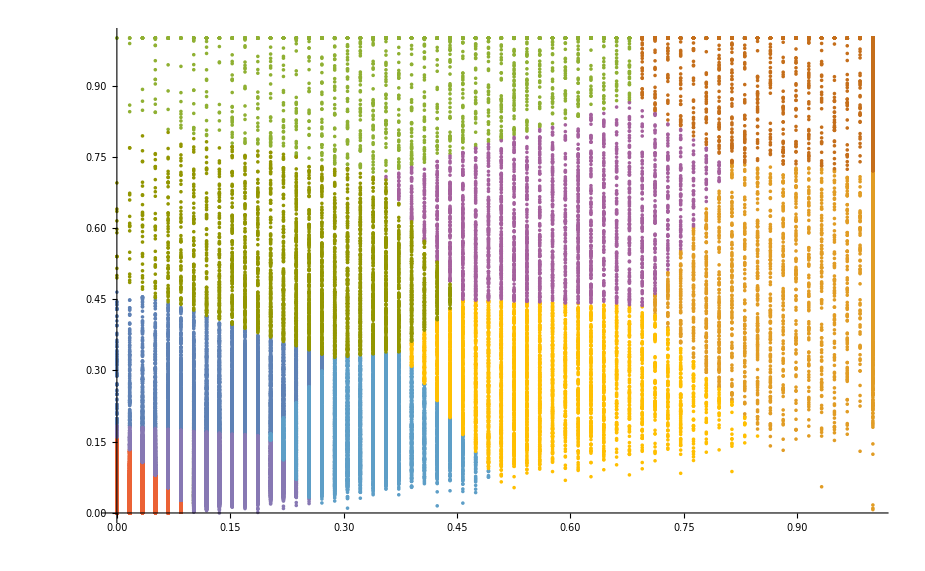

```mathematica
ListPlot[Values@KeyTake[assoFinal,#]&/@clusters]
```

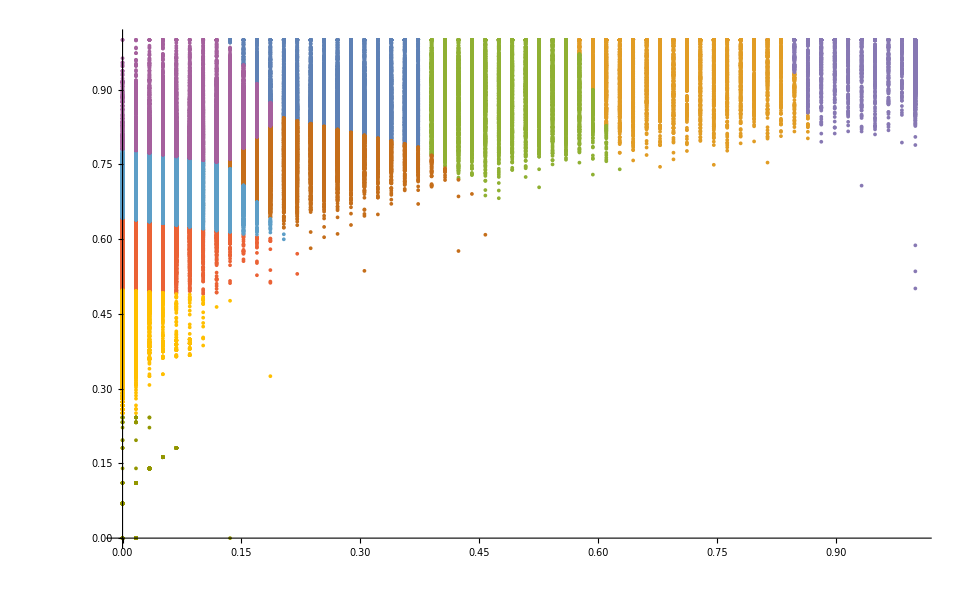

```mathematica
ListPlot[Values@KeyTake[assoFinalLog,#]&/@clustersLog]
```

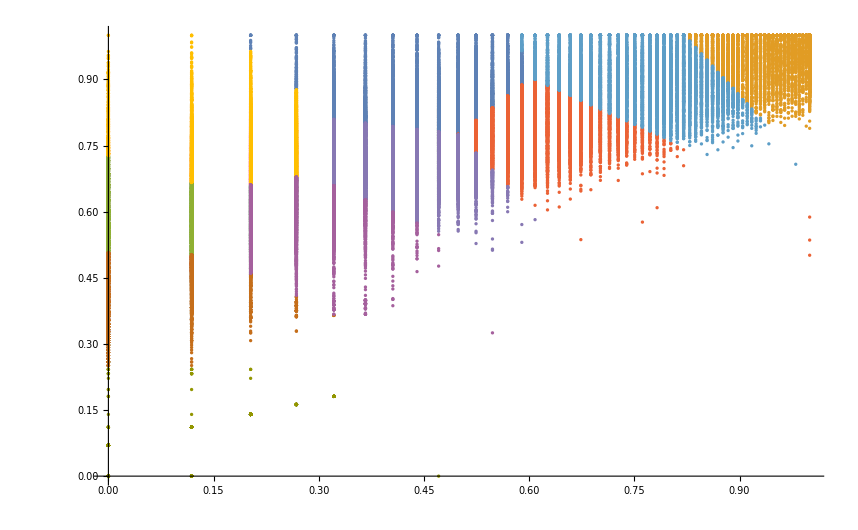

```mathematica
ListPlot[Values@KeyTake[assoFinalLog1,#]&/@clustersLog1]
```

## 其他

对特征进行分箱,平滑操作,聚类方法的选择等,有空再更新新例子.

本来就喜欢的记得点个赞

```mathematica
<<"/Users/hypergroups/Documents/Wolfram Mathematica/DeployProjects/MyMarkDown.m"
```

```mathematica
Notebook2Markdown[EvaluationNotebook[],"title"->"ColumnNormalize","dirOutput"->"/Users/hypergroups/Documents/Wolfram Mathematica/MyMarkdown/知乎专栏@Mathematica机器学习实战/"]
```

```mathematica
"/Users/hypergroups/Documents/Wolfram Mathematica/DeployProjects/MyMarkDown.m"//SystemOpen
```